# Tensor calculations with xAct

Edgar Gasperin

Instituto Superior Técnico
Oct 2024
Version: 17 Oct.

Instructions : do not execute the whole notebook at once . Each section is made independent with quit[] so if you try evaluating all at once it won’t work.

General Information and acknowledgements: 
In this notebook we give a general overview of the xAct package. It is intended to be a introductory lecture for people with no previous knowledge of xAct nor Mathematica. The discussion given in this notebook are based on my Mathematica notebooks and some examples inspired from projects with collaborators (Alfonso García-Parrado,  Juan Valiente Kroon, David Hilditch, Alex Vañó Viñuales). Other public resources that can be found in the official xAct webpage: http://www.xact.es/index.html

## Motivation

## What, Why, When and How.

### What is xAct?

-xAct : Efficient tensor computer algebra for the Wolfram Language developed by José M. Martín-García.
- Main contributors: Alfonso García-Parrado, Alessandro Stecchina, Barry Wardell, Cyril Pitrou, David Brizuela, David Yllanes, Guillaume Faye, Leo Stein, Renato Portugal, Teake Nutma, Thomas Bäckdahl.

### Why to use xAct?

-Some calculation in GR research nowadays can be very long and challenging.
-Reduce potential errors in very long calculations working on a robust computer algebra package.  -Tackle calculations with lots of terms which would seem overwhelming to do by hand.
-Becoming increasingly popular in GR research.

### When and when not to use xAct?

-There is a calculation which you understand and know how to do but seems overwhelming because it is very long?  If that is the case, use xAct!
-Is the calculation short and  isolated from a longer calculation/ research project (back-of-the-envelope type of calculation)? 
  If that is the case I’d recommend not to use xAct. 
-Is my calculation short but part of a bigger project (toy model)? 
If that is the case I’d recommend to use xAct.

### How?

-Short calculations which serve as a toy model for a longer calculations is the ideal arena to learn xAct.  The idea is to develop a general strateg  and identify the main mathematica rules and modules for an eventual longer calculation.
-Get some examples (several on the xAct website) to learn the basic rules and start writing your own notebook!

Further learning resources:

http://www.xact.es/xActCourse_Prague/

www.xact.es/Documentation/English/xActIntroduction_TeakeNutma.nb

https://github.com/xAct-contrib/examples/blob/master/README.md

https://groups.google.com/forum/#!forum/xAct

## Prerequisites

-Basic knowledge of tensor calculus.

-Basic knowledge of Mathematica is useful but by no means strictly fundamental. 
I believe one can learn the basics of Mathematica by working through examples in xAct. See for instance the examples given in this notebook.
  
  -Install Mathematica
  
  Install Mathematica on your computer.
   Some Universities and Research Institutions have Mathematica Licences for their Research Staff and Students. Ask your University if you can get one of these licences.
  
  https://www.wolfram.com/mathematica/pricing/students-individuals.php
  
  -Install xAct.
  
   Download the xAct bundle
  
  http://www.xact.es/download.html
  
  and read the installation notes. 
  
  
“... When uncompressed, the archive files give a number of files hanging from a directory called xAct/. This directory must be placed at (or linked from) one of the places Mathematica prepares for external
applications.  You can find the actual paths in your Mathematica installation in the variables $BaseDirectory and $UserBaseDirectory...”

```mathematica
$BaseDirectory 
$UserBaseDirectory
```

### What is contained in the xAct bundle

Diagram taken from Alfonso Garcia Parrado xAct Lectures.

See full lectures on
 http : // www.xact.es/xActCourse_Prague/

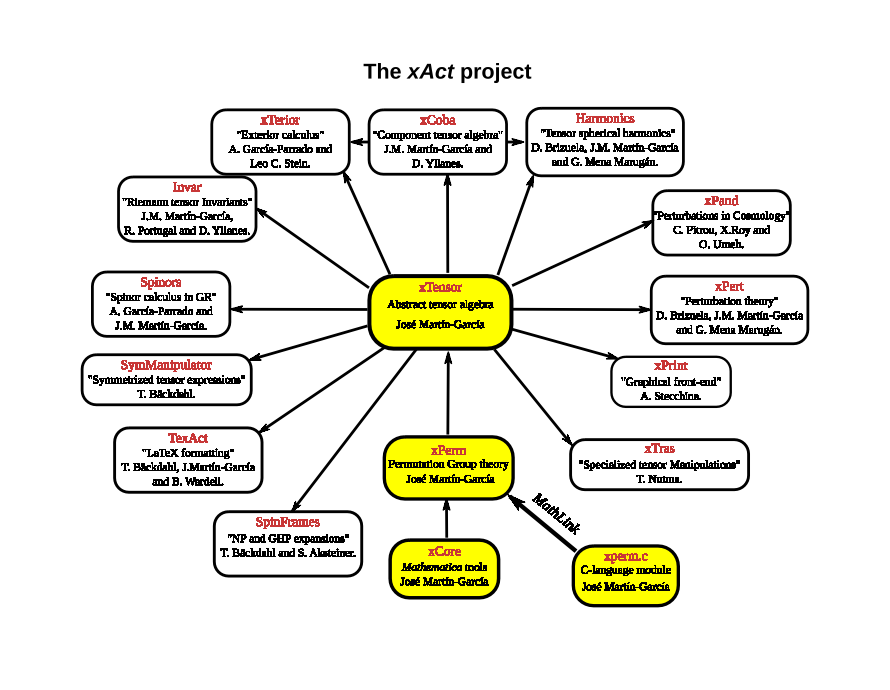

In this notebook we will mainly discuss xTensor and xCoba.

Why xTensor?

The xTensor package is the flagship of the system and, arguably, the ideal starting point to learn xAct.

Why xCoba?

This is one of the frequently asked questions is (see xTensor documentation) 

xTensor is great for abstract tensor calculus, but I want to do component computations. Can I do that with xTensor?

No, there is no support in xTensor for component tensor computer algebra. The twin package xCoba is being developed for that purpose, but it does not have the degree of maturity of xTensor.

Philosophy of this notebook: Experiential learning and hands on!

I believe that the best way to learn mathematics is to try things yourself.   
  Instead of a long discussion of the basics of Mathematica let me show you how to do some simple calculations with xTensor and xCoba that hopefully will get help you get started with your own notebook.

## xTensor and abstract calculations

If you want to do abstract tensor calculations xTensor is the package you are looking for

## The basics of xTensor

### Geometric playground

Load the xAct package

```mathematica
<<xAct`xTensor`
```

Define a manifold

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

Getting information: just put a question mark before the command and execute the cell.

```mathematica
?DefManifold
```

Define of a (Lorentzian) metric on the manifold

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
?DefMetric
```

Tensor notation : positive indices correspond to upper indices and negative indices to lower indices. 
xTensor: All indices are abstract!

We define tensors in the following way

```mathematica
DefTensor[VectorV[a],M4,PrintAs->"V"]
```

```mathematica
DefTensor[vec[a],M4,PrintAs->"w"]
```

```mathematica
DefTensor[CovectorJ[-a],M4,PrintAs->"J"]
```

```mathematica
DefTensor[F[-a,-b],M4,Antisymmetric[{-a,-b}]]
```

```mathematica
DefTensor[S[-a,-b],M4,Symmetric[{-a,-b}]]
```

```mathematica
DefTensor[ScalarPhi[],M4,PrintAs-> "ϕ"]
```

```mathematica
?DefTensor
```

### Example 1: Index gymnastics

Check that a tensor is antisymmetric.

```mathematica
F[-a,-b]+F[-b,-a]
ToCanonical[%]
```

Check that a tensor is symmetric.

```mathematica
S[-a,-b]
Symmetrize[%,{-a,-b}]
ToCanonical[%]
```

```mathematica
?ToCanonical
```

```mathematica
?Symmetrize
```

Raise and lower indices

```mathematica
g[a,b]S[-a,-c]
ContractMetric[%]
```

```mathematica
S[b, -c]
```

```mathematica
VectorV[-a]
SeparateMetric[g][%]
ScreenDollarIndices[%]
```

```mathematica
?ContractMetric
```

```mathematica
?SeparateMetric
```

Write this in the preamble of your notebook to avoid the ugly looking DollarIndices

```mathematica
$PrePrint=ScreenDollarIndices
```

```mathematica
VectorV[-a]
SeparateMetric[g][%]
```

### Example 2: Covariant derivatives and associated tensors

How to apply a covariant derivative

```mathematica
CD[-a]@VectorV[-b]
```

Look at  DefMetric . CD was defined as the Levi - Civita connection associated to g. 
Levi-Civita = Metric compatible and Torsion Free

```mathematica
CD[-a]@g[-b,-c]
```

```mathematica
HoldForm[CD[-a]@g[-b,-c]]
ReleaseHold[%]
```

```mathematica
HoldForm[CD[-a]@CD[-b]@ScalarPhi[]-CD[-b]@CD[-a]@ScalarPhi[]]
ReleaseHold[%]
```

How to commute covariant derivatives

```mathematica
CD[-a][CD[-b][VectorV[c]]]
SortCovDs[%,CD]
```

```mathematica
CD[-a]@CD[-b]@CD[-c]@VectorV[d]
CommuteCovDs[%,CD,{-b,-a}]
```

```mathematica
CD[-a]@CD[-b]@CD[-c]@VectorV[d]
CommuteCovDs[%,CD,{-c,-b}]
```

```mathematica
(* ?$RiemannSign *)
```

The curvature tensors

```mathematica
RiemannCD[-a,-b,-c,-d]
```

```mathematica
WeylCD[-a,-b,-c,-d]
```

```mathematica
RicciCD[-a,-b]
```

```mathematica
EinsteinCD[-a,-b]
```

```mathematica
RicciScalarCD[]
```

```mathematica
RiemannCD[-a,-b,-c,-d]
RiemannToWeyl[%]
RicciToEinstein@%
ToCanonical[%]
```

## Code Snippet : Wave equation for the Faraday Tensor

Exercise: Starting from the Maxwell equations (covariant equations for the  Faraday tensor) use the commands we have learned so far to derive the wave equation satisfied by the Faraday tensor

Although we have already introduced most of the objects we need. In this section I want to show you how a typical xAct calculation looks from beginning to end. So, I' ll introduce all the objects from the beginning so that you can read this section as a "stand alone".

We quit the kernel to quickly "erase" all of the definitions.

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
```

```mathematica
DefTensor[Faraday[-a,-b],M4,Antisymmetric[{-a,-b}],PrintAs->"F"]
```

```mathematica
Faraday[-a,-b]
```

The Maxwell equations

We write the Maxwell equations by hand.

```mathematica
GaussAmpereEq=CD[b]@Faraday[-b,-a]==0
GaussFaradayEq =Antisymmetrize[CD[-a]@Faraday[-b,-c],{-a,-b,-c}]==0
```

Notice that the second Maxwell equation can be simplified

```mathematica
ToCanonical[3*GaussFaradayEq]
```

To obtain the required wave equation one starts by applying a covariant derivative to the second Maxwell equation.

```mathematica
ToCanonical[GaussFaradayEq]
Expand[3*%]
CD[a]/@%
GaussFaradayEqALT=%
```

The first term is the D’Alembertian operator acting on F, the second and the third are not. We have to get rid of these terms.
Observe that if the second and third terms were a divergence ∇^b F |   |  
b | a we could use the first maxwell equations to kill those terms.

The standard trick is to commute covariant derivatives on these terms so that we get terms on which we can apply the first Maxwell equation.

```mathematica
GaussAmpereEq
```

```mathematica
GaussFaradayEqALT
SortCovDs[%,CD]
ToCanonical[%]
%/.ApplyRule@GaussAmpereEq
WaveEquationFaradayBasic=%
```

## More on covariant derivatives in xTensor

### Geometric playground

```mathematica
Quit[]
```

The standard prelude : we invoke xAct, define a Manifold, function to convert equations into rules  and define some tensors to play with.

```mathematica
<<xAct`xTensor`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
```

```mathematica
DefTensor[VectorV[a],M4,PrintAs->"V"]
```

```mathematica
DefTensor[vec[a],M4,PrintAs->"w"]
```

```mathematica
DefTensor[CovectorJ[-a],M4,PrintAs->"J"]
```

```mathematica
DefTensor[F[-a,-b],M4,Antisymmetric[{-a,-b}]]
```

```mathematica
DefTensor[S[-a,-b],M4,Symmetric[{-a,-b}]]
```

```mathematica
DefTensor[ScalarPhi[],M4,PrintAs-> "ϕ"]
```

Abstract indices!

Text taken from xAct' s documentation.

“ xTensor` performs abstract (coordinate-free) computations, so there is no real notion of chart in xTensor`. However, xTensor` has a PD operator, mainly to be able to convert covariant derivatives of tensors into "partial derivatives" of tensors plus Christoffel terms. Following Wald, we interpret PD as a arbitrary (but fixed) choice of a flat (zero curvature) and torsionless covariant derivative. Under such conditions, it is possible to find (at least locally) a coordinate system in which such PD covariant derivative corresponds directly to the partial derivatives with respect to the scalar fields of the chart. In that sense, the arbitrary choice of PD represents an arbitrary choice of chart, but we never specify any other chart in xTensor`, so there is no notion of "coordinate change". xTensor` is (by design) very limited regarding coordinate systems, precisely to make sure that all your computations are coordinate free. “

Any pair of covariant derivatives is related by a Christoffel “tensor”, we can handle routinely Christoffel tensors relating two  derivatives.

### Example 3: Levi-Civita and general connections

PD derivative of a covector

```mathematica
PD[-a]@vec[-b]
```

ChangeCovD will allow you to transit from a covariant derivative to another one .

```mathematica
CD[-a]@vec[-b]
ChangeCovD[%,CD, PD]
(*if you don't know the name of a tensor that xAct has "generated" use InputForm *)
%//ScreenDollarIndices;
InputForm[%]
```

xAct is not limited to Levi - Civita connections,  it allows for more general covariant derivatives (with torsion and not compatible with the metric!)

```mathematica
DefCovD[othercd[-a],Torsion->True,SymbolOfCovD->{"|","OverTilde[∇]"}]
```

```mathematica
othercd[-a]@g[-b,-c]
ToCanonical[%]
```

```mathematica
HoldForm[othercd[-a]@othercd[-b]@ScalarPhi[]-othercd[-b]@othercd[-a]@ScalarPhi[]]
ReleaseHold[%]
%//TorsionToChristoffel
```

So we have so far 3 derivatives : PD, CD (which  have been predefined for us inside xAct once we assume there exist a metric on the manifold) and othercd which we have just introduced .

Relation between  othercd and PD or CD? Use ChangeCovD

```mathematica
othercd[-a]@vec[-b]
ChangeCovD[%,othercd,CD]
```

Levi - Civita connection in terms of PD derivatives of the metric (an instance of the Koszul formula)

```mathematica
ChristoffelCD[c,-a,-b]
ChristoffelToMetric[%]
```

Each connection has an associated curvature

To write the Curvature in terms of derivatives of the connection use  ChangeCurvature

```mathematica
RiemannCD[-a,-b,-c,-d]
ChangeCurvature[%,CD,PD]
```

We passed from  R[∇] |   |   |   |  
a | b | c | d to R[∂]_abcd (which is zero by definition of the PD derivative)

For a general non-Levi-Civita connection the action of ChangeCurvature is more clear .

```mathematica
Riemannothercd[-a,-b,-c,-d]
ChangeCurvature[%,othercd,CD]
```

Notice the derivatives of the connection terms (Γ[∇,OverTilde[∇]]) appearing  are not PD derivatives they are  ∇-derivatives and not ∂.
We passed from R[OverTilde[∇]] |   |   |   |  
a | b | c | d to   R[∇] |   |   |   |  
a | b | c | d.

### Example 4: Verifying the second Bianchi identities

Verify the  second Bianchi identity for the curvature R[∇] associated to the Levi-Civita connection. In other words show that
∇_([f) R[∇]_(|a|bcd]) =0  by rewriting the curvature as derivatives of Γ and then  Γ as derivatives of the metric

```mathematica
(* write the relevant expreesion antisymmetrised *)
CD[-f][RiemannCD[-a,-b,-c,-d]]
Antisymmetrize[%,{-c,-d,-f}]
%//ToCanonical
(* Change Riemann by CD derivatives by PD derivatives. This can be done using ChangeCovD as we learned before or CovDToChristoffel *)
%//CovDToChristoffel
(* Express the curvature in terms of derivatives of Γ *)
ChangeCurvature[%,CD]
(* Grab the last calculation and then express Γ in terms of derivatives of the metric*)
ChristoffelToMetric[%,g]
%//ScreenDollarIndices
(* This gives a terribly long expression which should cancel out if one uses the symmetries and relables dummy indices. All done
automatically using ToCanonical*)
%//ToCanonical
```

## Code Snippet: Hyperbolic Reduction of the Vacuum Einstein field equation in Harmonic Gauge

Exercise: Obtain the reduced Einstein field equations in Harmonic Gauge .
This shows the example of a self contained calculation from beginning to end.

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
(*ApplyRuleNoIndexMove[expr_]:=MakeRule[Evaluate[List@@expr]]*)
```

Context : The Ricci = 0 equations do not have a definite PDE character (hyperbolic, elliptic or parabolic) unless a gauge is fixed .
 Yvonne Choquet - Bruhat showed that in harmonic gauge (wave coordinates) the EFE become a system of wave equations for the metric (hyperbolic reduction) .

Harmonic gauge is characterised by the condition that the contracted Christoffel symbols vanishΓ[∇] | c |   |  
  | a | b g | a | b
  |   =0

Strategy : define the Reduced Ricci tensor as the Ricci tensor minus a symmetrised derivative of the contracted Christoffel symbols and show that Reduce Ricci = 0 gives a system of wave equations for the metric

```mathematica
DefTensor[ReducedRicciTensor[-a,-b],M4,PrintAs->"R^-"]
```

```mathematica
DefTensor[ContractedChristoffel[-a],M4,PrintAs->"Γ"]
```

```mathematica
ContractedChristoffelDefinition=ContractedChristoffel[c]==g[a,b]ChristoffelCD[c, -a, -b]
```

```mathematica
ReducedRicciTensorDefinition=ReducedRicciTensor[-a,-b]==RicciCD[-a,-b]-Symmetrize[CD[-a][ContractedChristoffel[-b]],{-a,-b}]
```

If the Harmonic Coordinate condition is satisfied then the contracted Christoffel symbols vanish and the reduced Ricci tensor and the Ricci tensor coincide. Thus if we impose the EFE in vacuum R[∇] |   |  
a | b= 0 and impose the harmonic coordinate condition Γ |  
b=0 is satisfied (and its derivatives), then the Reduced Ricci tensor must vanish R^- |   |  
a | b =0.

```mathematica
DefTensor[ReducedWaveOperatorMetric[-a,-b],M4,PrintAs->"OverTilde[□]g"]
```

Definition of the reduced wave operator

```mathematica
ScreenReducedWaveOperator=g[c,d]PD[-c][PD[-d][g[-a,-b]]]==ReducedWaveOperatorMetric[-a,-b]
```

The reason for the use of the Reduced Wave operator instead of the Geometric wave operator -- - the one defined with ∇ instead of  ∂ --- is that if the metric is an unknown then derivatives of the connection represent second derivatives of the metric and that can alter the principal part of the operator. The difference between OverTilde[□] and □ acting on a tensor contain derivatives of the connection.

```mathematica
ReducedRicciTensor[-a,-b]==0
(* write Reduce Ricci =0  and apply the definitions*)
%/.ApplyRule@ReducedRicciTensorDefinition
%/.ApplyRule@ContractedChristoffelDefinition
(* Express everything in terms of derivatives of the metric *)
ChangeCovD[%,CD, PD]
ChangeCurvature[%,CD,PD]
ChristoffelToMetric[%,g]
ContractMetric[%];
ToCanonical[%]
(* To have a nice printing identity the second order derivatives of the metric and see they form the reduce wave operator *)
%/.ApplyRule@ScreenReducedWaveOperator
Solve[%,ReducedWaveOperatorMetric[-a,-b]];
(* turn rule into an equation *)
Equal@@First@Flatten@%;
ReducedEFEharmonic=%
```

```mathematica
ReducedEFEharmonic
```

This equation is hyperbolic, all the second derivatives of the metric are on the LHS and they form part of a hyperbolic operator . The RHS only contains first derivatives of the metric square.

## xCoba and component calculations

If you want to do component calculations xCoba is the package you are looking for.

## xCoba basic notions

Same preamble as usual

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
```

```mathematica
<<xAct`xCoba`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
```

```mathematica
DefTensor[ScalarPhi[],M4,PrintAs->"ϕ"]
DefTensor[VectorV[a],M4,PrintAs->"V"]
DefTensor[CovectorJ[-a],M4,PrintAs->"J"]
DefTensor[F[-a,-b],M4,Antisymmetric[{-a,-b}]]
DefTensor[S[-a,-b],M4,Symmetric[{-a,-b}]]
```

The new object that xCoba gives access are coordinate charts

Declare chart called myChart:

Choose a colour for your coordinate indices . If nothing is specified then red is the colour of the associated coordinate indices

Note that coordinates are scalar fields, and hence need a pair of brackets.

```mathematica
DefChart[myChart,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]} (*,FormatBasis->{"Partials","Differentials"}*)]
```

Declare  another chart :

Choose a colour for your coordinate indices.

```mathematica
DefChart[MyCOordinates,M4,{0,1,2,3},{T[],R[],S[],Z[]} ,ChartColor->RGBColor[0,0,1](*,FormatBasis->{"Partials","Differentials"}*)]
```

Coordinate (Frame) Indices Notation.

This is an abstract vector and not a component! xTensor = abstract.

```mathematica
VectorV[a]
```

This represents the components of the vector V | a
  in the coordinate basis associated to B.  xCoba= Components!

```mathematica
VectorV[{a,myChart}]
```

This represents the components of the vector V | a
  in the coordinate-basis associated to MyCOordinates.

```mathematica
VectorV[{a,MyCOordinates}]
```

The latter object is not a vector! it is a collection of scalars associated to a particular basis . This collection of scalars contains the following scalars

```mathematica
VectorV[{0,myChart}]
VectorV[{1,myChart}]
VectorV[{2,myChart}]
VectorV[{3,myChart}]
```

To denote the components of a covector respect to the cobasis associated to a given coordinate system the notation is as follows . 
  Notice that the minus sign is not on the index but on the name of the Basis/Coordinates

```mathematica
VectorV[{a,-myChart}]
(*VectorV[{-a,myChart}]
VectorV[{-a,-myChart}]*)
```

```mathematica
VectorV[{0,-MyCOordinates}]
```

```mathematica
VectorV[{0,-myChart}]
VectorV[{1,-myChart}]
VectorV[{2,-myChart}]
VectorV[{3,-myChart}]
```

Similar notation is true for components of tensors

```mathematica
S[{a,-MyCOordinates},{b,-MyCOordinates}]
```

```mathematica
S[{a,-myChart},{b,-myChart}]
S[{a,myChart},{b,myChart}]
S[{a,myChart},{b,-myChart}]
```

Basis Vectors:  Abstract vs Coordinate (or frame) Indices

```mathematica
(*HoldForm[PD[-a]@r[]]
ReleaseHold[%]
InputForm[%]*)
```

The basis vectors are written as:

```mathematica
Basis[{-a,-myChart},c]
ComponentArray[%]
```

Notice basis vectors have an abstract index upstairs to indicate they are vectors . Black indices are abstract . The lower Red index in the basis vector is a coordinate or frame index .

Careful when using “numeric coordinate” indices

```mathematica
{Basis[{0,-myChart},a],Basis[{1,-myChart},a],Basis[{2,-myChart},a],Basis[{3,-myChart},a]}
```

Dual Co-Basis

```mathematica
Basis[{a,myChart},-a]
ComponentArray[%]
```

Using "numeric coordinate" indices

```mathematica
{Basis[{0,myChart},-a],Basis[{1,myChart},-a],Basis[{2,myChart},-a],Basis[{3,myChart},-a]}
```

The co - basis vectors acting on the basis vectors gives the identity . Notice that the repeated indices are abstract so there is no summation implied because abstract indices do not represent components!

```mathematica
Basis[{a,myChart},-c]Basis[{-b,-myChart},c]
ContractBasis[%]
ComponentArray[%]
%//MatrixForm
```

When using coordinate indices, repeated up - down indices indicate a summation .

```mathematica
Basis[{a,myChart},-c]Basis[{-a,-myChart},d]
%//TraceBasisDummy
```

An tensor can be expressed in terms of its components respect to a coordinate basis and tensor products of the coordinate basis vectors and covectors

```mathematica
S[-a,-b]
SeparateBasis[myChart][%]
TraceBasisDummy[%]
```

Re - writing an abstract index in terms of components respect to a basis .

```mathematica
S[-a,-b]
ToBasis[myChart][%]
```

Derivatives

At first sight making a difference between abstract and coordinate indices may look unnecessary but there are fundamental differences that are made evident when dealing with derivatives.

Components of such abstract object in a particular coordinate basis

```mathematica
CD[{-a,-myChart}][ScalarPhi[]]
SeparateBasis[AIndex][%]
```

Acting on scalars the CD and PD derivative coincide . 
  Use ChangeCovD to corroborate this fact .

```mathematica
CD[{-b,-myChart}] @ScalarPhi[]
ChangeCovD[%,CD,PD]
```

IMPORTANT EXAMPLE!   What is the ∇_a  derivative of  V |  
b notice that the index is red.

```mathematica
CD[{-a,-myChart}][VectorV[-{b,-myChart}]]
ChangeCovD[%,CD,PD]
```

Question for the audience:  Is xAct wrong?

Contrast with the abstract calculation

```mathematica
CD[-a][VectorV[-b]]
ChangeCovD[%,CD,PD]
```

Is xAct wrong?  No! 
Why? because V |  
b is just a scalar. It is not a covector! and the covariant derivative acting on a scalar is just a partial derivative.

The correct way to think of this calculation in xAct is then the following .
  First create an abstract object . All is safe and coordinate independent .
  Then  obtain its components .

```mathematica
Basis[{-c,-myChart},a]Basis[{-d,-myChart},b]CD[-a][VectorV[-b]]
SeparateBasis[myChart][%]
ChangeCovD[%,CD,PD]
ContractBasis[%]
```

Assigning  values to tensor components.

```mathematica
ComponentValue[VectorV[{0,-myChart}],r[]^2]
ComponentValue[VectorV[{1,-myChart}],Sqrt[Log[r[]]]]
ComponentValue[VectorV[{2,-myChart}],Tan[θ[]]^(1/3)]
ComponentValue[VectorV[{3,-myChart}],3]
```

```mathematica
VectorV[-a]
SeparateBasis[-myChart][%]
TraceBasisDummy[%]
ToValues[%]
```

One can define general non-coordinate bases for example

```mathematica
DefBasis[GeneralBasis,TangentM4,{0,1,2,3},BasisColor->RGBColor[0,1,1]]
```

Move from the red basis to the green basis

```mathematica
Basis[{-a,-myChart},c]
SeparateBasis[GeneralBasis][%]
TraceBasisDummy[%]
```

In the case of coordinate basis this object with two colour indices encodes the Jacobian of the transformation.
However xAct allows to work with non-holonomic bases  (namely non coordinate) for which e |   | b
a |   represents the frame coefficient relating the two bases.
Non-holonomic bases are referred in GR as “Veilbeins” or “Tetrads”.

```mathematica
Basis[{-a,-myChart},{b,GeneralBasis}]
```

```mathematica
SomeMatrix={{1,1,2,r[]t[]},{1,0,θ[],Sin[r[]t[]]},{r[]^5,t[]*Log[Sin[θ[]]],3,1},{1,t[]^4,3,2}}
%//MatrixForm
```

```mathematica
AllComponentValues[Basis[{-a,-myChart},{b,GeneralBasis}], SomeMatrix]
```

```mathematica
Basis[{2,-myChart},c]
SeparateBasis[GeneralBasis][%]
TraceBasisDummy[%]
ToValues[%]
```

## Code Snippet : Wave equation on a fixed background

This is the example you should be looking for if you want to make calculations of the type : given an explicit metric with explicit coordinates compute Ricci, Riemann, Christoffels etc. The key command to do this automatically is MetricCompute. 
There are other programs (Maple, SageManifolds) where these type of calculations can be carried out. 
However, recall that  xAct’s power resides on its capability of performing abstract and coordinate free calculations! --xTensor!

### Minkowski

This is a basic example of the calculation of the components of tensors given a metric and coordinate basis on which the metric is written using MetricCompute.
We use the results to obtain the expression for the wave equation in the given spacetime background using the commands we learned before.

Input the metric.

```mathematica
MatrixForm[MetricInCoordBasis={
{-1,0,0,0},
{0,1,0,0},
{0,0,r[]^2,0},
{0,0,0,r[]^2 Sin[θ[]]^2}
}]
```

We simply pass the components matrix as third argument. Note the minus sign in front of B. This indicates that we are supplying the covariant components of the metric.

```mathematica
?MetricInBasis
```

```mathematica
MetricInBasis[g,-myChart,MetricInCoordBasis]
```

```mathematica
?MetricCompute
```

```mathematica
MetricCompute[g,myChart,"Metric"[1,1],CVSimplify->Simplify]
Last@TensorValues[g]
```

```mathematica
MetricCompute[g,myChart,"Christoffel"[1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[ChristoffelCDPDmyChart]
```

Now we compute a particular object. We can choose, with the option CVSimplify, the function which is used on all (independent) components after each step of the computation.    To see the possible values for the third argument simply write the symbol All there. Note the structure string[1, -1, ...] , where - 1 means covariant and 1 means contravariant.

Check that Minkowski is a Flat

```mathematica
MetricCompute[g,myChart,"Riemann"[-1,-1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[RiemannCD]
```

Wave equation in flat space in spherical Coordinates

```mathematica
g[a,b]CD[-a]@CD[-b]@ScalarPhi[]==0
ToBasis[myChart][%]
TraceBasisDummy/@%
ToValues[%]
ChangeCovD[%,CD,PD]
FlatWaveEquation=%;
```

### Kerr Newman

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
```

```mathematica
<<xAct`xCoba`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
```

```mathematica
DefTensor[ScalarPhi[],M4,PrintAs->"ϕ"]
```

Now lets do the same for Kerr Newman.

First, declare some constants to be used in the metric in the coordinate system.

```mathematica
DefConstantSymbol[Mass,PrintAs->"M"]
DefConstantSymbol[Rotation,PrintAs->"a"]
DefConstantSymbol[Charge,PrintAs->"Q"]
```

```mathematica
Delta=r[]^2+Rotation^2+Charge^2-2Mass r[];
Sigma=r[]^2+Rotation^2Cos[θ[]]^2;
```

```mathematica
MatrixForm[KerrMetric={
{-(Delta-Rotation^2Sin[θ[]]^2)/Sigma,0,0,-Rotation Sin[θ[]]^2(r[]^2+Rotation^2-Delta)/Sigma},
{0,Sigma/Delta,0,0},
{0,0,Sigma,0},
{-Rotation Sin[θ[]]^2(r[]^2+Rotation^2-Delta)/Sigma,0,0,((r[]^2+Rotation^2)^2-Delta Rotation^2Sin[θ[]]^2)/Sigma Sin[θ[]]^2}
}]
```

```mathematica
DefChart[B,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

```mathematica
MetricInBasis[g,-B,KerrMetric]
```

```mathematica
MetricCompute[g,B,"Metric"[1,1],CVSimplify->Simplify]
Last@TensorValues[g]
```

```mathematica
TensorValues[g]
```

```mathematica
MetricCompute[g,B,"Christoffel"[1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[ChristoffelCDPDB]//Column
```

```mathematica
MetricCompute[g,B,"Riemann"[-1,-1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[RiemannCD]//Column
```

```mathematica
MetricCompute[g,B,"Ricci"[-1,-1],CVSimplify->Simplify]
Last@TensorValues[RicciCD]//Column;
(*Verify that you get a vacuum solution when the charge vanishes *)
%/.Charge->0
```

Wave equation on Kerr.

```mathematica
g[a,b]CD[-a]@CD[-b]@ScalarPhi[]==0
ToBasis[B][%]
TraceBasisDummy/@%
ToValues[%]
(**setting charge to zero **)
%/.Charge->0;
ChangeCovD[%,CD,PD];
KerraveEquation=%
```

### Spherically symmetric metric

```mathematica
Quit[]
```

```mathematica
<<xAct`xTensor`
```

```mathematica
<<xAct`xCoba`
```

```mathematica
DefManifold[M4,4,{a,b,c,d,f,p,q,l,h,j,n}]
```

```mathematica
DefMetric[-1,g[-a,-b],CD,{";","∇"}]
```

```mathematica
$PrePrint=ScreenDollarIndices;
```

```mathematica
ApplyRule[expr_]:=MakeRule[Evaluate[List@@expr],MetricOn->All,ContractMetrics->True]
```

```mathematica
DefTensor[ScalarPhi[],M4,PrintAs->"ϕ"]
```

Choose the coordinate basis

```mathematica
DefChart[CoordBasis,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->RGBColor[0,0,1]]
```

```mathematica
(*DefConstantSymbol[Mass,PrintAs->"M"]*)
```

```mathematica
(*DefScalarFunction[V]*)
```

```mathematica
(*DefScalarFunction[U]*)
```

```mathematica
DefScalarFunction[F]
```

```mathematica
DefScalarFunction[G]
```

```mathematica
(*MatrixForm[MetricInCoordBasis={
{Exp[2V[t[],r[]]],0,0,0},
{0,-Exp[2U[t[],r[]]],0,0},
{0,0,-r[]^2,0},
{0,0,0,-r[]^2 Sin[θ[]]^2}
}]*)
```

Introduce the metric in the coordinate basis

```mathematica
MatrixForm[MetricInCoordBasis={
{F[t[],r[]]^2,0,0,0},
{0,-G[t[],r[]]^2,0,0},
{0,0,-r[]^2,0},
{0,0,0,-r[]^2 Sin[θ[]]^2}
}]
```

```mathematica
MetricInBasis[g,-CoordBasis,MetricInCoordBasis]
```

Compute the Christoffel symbols in the coordinate basis

```mathematica
(*MetricCompute[g,CoordBasis,"Christoffel"[1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[ChristoffelCDPDCoordBasis]*)
```

```mathematica
MetricCompute[g,CoordBasis,"Christoffel"[1,-1,-1],CVSimplify->Simplify]
Last@TensorValues[ChristoffelCDPDCoordBasis]//Column;
```

```mathematica
MetricCompute[g,CoordBasis,"Riemann"[-1,-1,-1,-1],CVSimplify->Simplify]
```

Most of the time is spent in the simplification of the tensor components.

Now we have the independent components :

```mathematica
Last@TensorValues[RiemannCD]//Column;
```

```mathematica
MetricCompute[g,CoordBasis,"Ricci"[-1,-1],CVSimplify->Simplify]
Last@TensorValues[RicciCD]//Column;
```

```mathematica
MetricCompute[g,CoordBasis,"RicciScalar"[],CVSimplify->Simplify]
Last@TensorValues[RicciScalarCD]//Column
```

```mathematica
g[a,b]CD[-a]@CD[-b]@ScalarPhi[]==0
ToBasis[CoordBasis][%];
TraceBasisDummy/@%
ToValues[%];
ChangeCovD[%,CD,PD];
WaveEquationSphericallySymmetricBackground=%
```

## Further resources

Further information and more lectures can be found in

 http://www.xact.es/index.html 
 
 www.xact.es/Documentation/English/xActIntroduction_TeakeNutma.nb
 
 http : // www.xact.es/xActCourse_Prague/
  
  http://www.xact.es/documentation.html
 
  https://groups.google.com/forum/#!forum/xAct